```mathematica
`
```

# Machine Learning

## Wolfram Data Repository

## Black and White Images

```mathematica
ResourceObject["FER-2013"]
```

ResourceObject[…]

## Color Images

```mathematica
ResourceObject["CIFAR-10"]
```

ResourceObject[…]

## What are Images ?

### A black and white image is described as a matrix, with values 0 to 1

Zero being white and One being black.

```mathematica
blackAndWhite = Table[RandomInteger[1],{i,3},{j,3}] ;
```

```mathematica
TraditionalForm[MatrixForm[blackAndWhite]]
```

(1 | 1 | 1
0 | 0 | 0
0 | 0 | 1)

#### Plotting Matrices

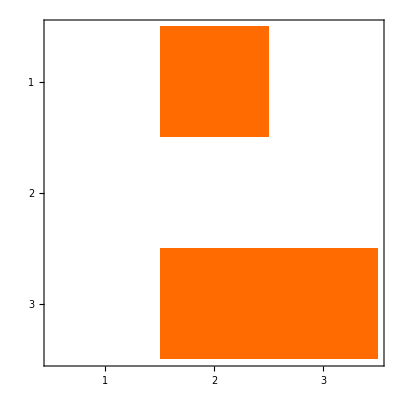

```mathematica
MatrixPlot[blackAndWhite]
```

### Color Images Are Described with Tensors

#### Simple Version

```mathematica
TraditionalForm[MatrixForm[ Table[RandomInteger[1],{i,3},{j,3}]]]
```

(0 | 0 | 0
0 | 0 | 1
0 | 1 | 1)

#### Full Example

```mathematica
colorImage =Table[ Table[RandomInteger[255],{i,3},{j,3}],{i,3},{j,3}];
```

```mathematica
TraditionalForm[MatrixForm[colorImage]]
```

((198 | 144 | 115
64 | 234 | 171
106 | 40 | 229) | (247 | 135 | 148
78 | 35 | 203
200 | 71 | 2) | (50 | 140 | 190
123 | 230 | 131
3 | 212 | 208)
(58 | 234 | 21
229 | 253 | 164
102 | 214 | 150) | (240 | 54 | 64
200 | 24 | 67
64 | 166 | 233) | (97 | 14 | 58
253 | 76 | 226
147 | 183 | 140)
(23 | 230 | 236
45 | 251 | 134
231 | 115 | 129) | (110 | 204 | 231
9 | 23 | 132
221 | 225 | 11) | (113 | 96 | 51
227 | 62 | 149
117 | 150 | 243))

#### A Tensor can be described with a sparse array.

```mathematica
sparse = SparseArray[colorImage]
```

SparseArray[…]

```mathematica
sparse["Properties"]//MatrixForm
```

(AdjacencyLists
Background
ColumnIndices
Density
MatrixColumns
NonzeroValues
PatternArray
Properties
RowPointers)

## Data for our Machine Learning Models

```mathematica
allData =  RandomSample[ResourceData["FER-2013"],500];
```

```mathematica
allColorData = Import[NotebookDirectory[]<>"/data/colorAnimals.m"];
```

### Data Wrangling (Munging)

```mathematica
allColorData⟦1;;5⟧
```

{-Graphics-→deer,-Graphics-→frog,-Graphics-→airplane,-Graphics-→cat,-Graphics-→frog}

Look at the data that we have in our dataset.

```mathematica
DeleteDuplicates[Last[allColorData⟦#⟧]&/@Range[Length[allColorData]]]
```

{deer,frog,airplane,cat,ship,bird,truck,dog,automobile,horse}

#### Restrictions

```mathematica
myRestrictions = {"cat","dog","horse","deer","frog","bird"};
```

```mathematica
g[x_]:=Select[allColorData,Last[#]==x&];
```

```mathematica
readyData = Flatten[g[#]&/@myRestrictions];
```

```mathematica
readyData//Length
```

601

#### Pattern Matching Example

```mathematica
colorImages = Cases[allColorData,HoldPattern[_->#]]&/@myRestrictions;
```

```mathematica
finalColorPrepData = Flatten[colorImages];
```

## Image Processing

```mathematica
A = allData[[1]]
```

-Graphics-→sadness

```mathematica
First[A]
```

-Graphics-

### Image Functions

```mathematica
Animate[Binarize[First[A],r],{r,0,1,0.1}]
```

### List of Image Functions

```mathematica
house = ExampleData[{"TestImage","House"}]
```

-Graphics-

```mathematica
HistogramTransform[house]
```

-Graphics-

```mathematica
ColorQuantize[house,4]//ImageAdjust
```

-Graphics-

```mathematica
EdgeDetect[house]
```

-Graphics-

```mathematica
Animate[ColorQuantize[house,n,Dithering->False]-EdgeDetect[house],{n,1,20,1}]
```

```mathematica
DominantColors[house]
```

{RGBColor[0.6179548174327589, 0.773418730383829, 0.8688828392911802],RGBColor[0.6595244425699881, 0.4271383455568531, 0.39849783908433695],RGBColor[0.4813593607166102, 0.36722117798938353, 0.411243892126088],RGBColor[0.8549496449365236, 0.8970788768716457, 0.8847619654299778],RGBColor[0.41988990431663153, 0.5373913981838716, 0.6481610879401098]}

```mathematica
rawImage = ClusteringComponents[ColorConvert[house,"Grayscale"],3];
```

```mathematica
Manipulate[func[rawImage],{func,{ArrayPlot,MatrixPlot}}]
```

```mathematica
Animate[
Colorize@ClusteringComponents[ColorConvert[house,"Grayscale"],n],{n,1,100,1}]
```

## Analyse

#### Get A Certain Range of Emotions

```mathematica
emotions = {
Entity["Emotion","Happiness::d8973"],
Entity["Emotion","Neutral::7468h"],
Entity["Emotion","Sadness::t2566"],
Entity["Emotion","Anger::bb6bt"],
Entity["Emotion","Surprise::dj3w9"],
Entity["Emotion","Disgust::s4t7h"],
Entity["Emotion","Fear::7k5tk"]
};
```

```mathematica
emotions⟦1⟧ //FullForm
```

Entity["Emotion","Happiness::d8973"]

#### Function for specified Images

```mathematica
images = Cases[allData,HoldPattern[_->#]]&/@emotions;
```

```mathematica
finalPrep = Flatten[images];
```

#### Splitting Data

```mathematica
Length[finalPrep]
```

500

```mathematica
splitter[20]
```

splitter[20]

```mathematica
splitter[x_] := Floor[Length[finalPrep] * x/(100)];
```

```mathematica
randomOrder = RandomSample[allData];
```

Split Data into training set and test set.

```mathematica
trainingData =Take[randomOrder,splitter[80]];
```

```mathematica
testData = Drop[randomOrder,splitter[80]];
```

```mathematica
distribution = PieChart[{Length[trainingData],Length[testData]},ChartLabels->{"Training Data","Test Data"}]
```

-Graphics-

#### Built-in Machine Learning Model

```mathematica
builtIn = Classify["FacialExpression"];
```

#### Build Your Own Classifier

```mathematica
classifier = Classify[trainingData,TargetDevice->"CPU",Method->"GradientBoostedTrees",PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

#### Information about Classifier

```mathematica
Information[classifier]
```

Classifier information
Data type | Image
Number of classes | 7
Accuracy | (29.4.) %
Method | LogisticRegression
Single evaluation time | 117. ms/example
Batch evaluation speed | 8.06 examples/s
Loss | 1.78 ± 0.069
Model memory | 329. kB
Training examples used | 400 examples
Training time | 1 26
 |

#### Testing our Classifier Model

```mathematica
testData[[4]]
```

-Graphics-→fear

```mathematica
classifier[First@testData[[4]]]
```

happiness

```mathematica
classifier[First[testData[[4]]],"TopProbabilities"]
```

{happiness→0.27691,fear→0.175069,sadness→0.164622,surprise→0.161378,anger→0.151707,neutral→0.0509409}

#### Classifier Application

```mathematica
Manipulate[
GraphicsRow[
{
TableForm@classifier[First[testData[[i]]],"TopProbabilities"],
First[testData⟦i⟧],
BarChart[Association@classifier[First[testData⟦i⟧],"TopProbabilities"]]
},ImageSize->Full],
{i,1, Length[testData],1}]
```

Part::partd: Part specification testData⟦19⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

BarChart::ldata: Association[classifier[First[testData⟦FE`i$$27⟧],TopProbabilities]] is not a valid dataset or list of datasets.

Part::partd: Part specification testData⟦19⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

BarChart::ldata: Association[classifier[First[testData⟦FE`i$$43⟧],TopProbabilities]] is not a valid dataset or list of datasets.

#### Get Statistical Information about your classifier

```mathematica
cm= ClassifierMeasurements[classifier,testData]
```

ClassifierMeasurementsObject[…]

#### Using Test Data

```mathematica
cm["Accuracy"]
```

0.19

```mathematica
Manipulate[cm[prop],{{prop,"ConfusionMatrixPlot","Properties"},cm["Properties"]}]
```

## Color Image Example

#### Data Wrangling

```mathematica
allColorData⟦1;;5⟧
```

{-Graphics-→deer,-Graphics-→frog,-Graphics-→airplane,-Graphics-→cat,-Graphics-→frog}

```mathematica
DeleteDuplicates[Last[allColorData⟦#⟧]&/@Range[Length[allColorData]]]
```

{deer,frog,airplane,cat,ship,bird,truck,dog,automobile,horse}

Create groups of specefic....

```mathematica
myRestrictions = {"cat","dog","horse","deer","frog","bird"};
```

```mathematica
colorImages = Cases[allColorData,HoldPattern[_->#]]&/@myRestrictions;
```

```mathematica
finalColorPrepData = Flatten[colorImages];
```

#### Create Classifier

```mathematica
c = Classify[finalColorPrepData]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Image
Number of classes | 6
Accuracy | (78.5.) %
Method | LogisticRegression
Single evaluation time | 114. ms/example
Batch evaluation speed | 8. examples/s
Loss | 0.677 ± 0.088
Model memory | 310. kB
Training examples used | 601 examples
Training time | 2 0
 |

#### Testing Images

```mathematica
testModel= -Graphics-;
```

```mathematica
testCat = -Graphics-;
```

```mathematica
testBird = First[finalColorPrepData⟦Length[finalColorPrepData]⟧]
```

#### Testing Model

dog

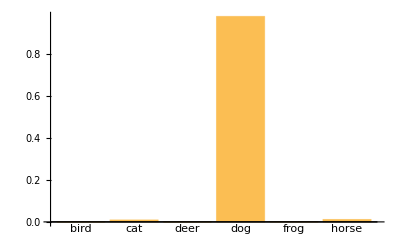

{dog→0.675033,cat→0.302744}

```mathematica
c[testModel] 
BarChart[c[testModel,"Probabilities"],ChartLabels->Automatic]
c[testCat,"TopProbabilities"]
```

```mathematica
c[testBird]
```

#### Measurements

```mathematica
measurements = ClassifierMeasurements[c,testData]
```

```mathematica
Manipulate[measurements[x],{x,measurements["Properties"]}]
```